```mathematica
data=Import[NotebookDirectory[]<>"../data/volt_sigmas.txt","Table"]
```

{{0.0000173659,2.61768×10^-6},{0.0000152069,2.18363×10^-6},{0.0000137475,1.88555×10^-6},{0.0000124575,1.63162×10^-6},{0.000011351,1.39909×10^-6},{0.0000105196,1.25975×10^-6},{9.8639×10^-6,1.14729×10^-6},{9.24933×10^-6,1.04256×10^-6},{8.77747×10^-6,9.62736×10^-7},{8.32645×10^-6,8.88955×10^-7},{8.18261×10^-6,8.64491×10^-7}}

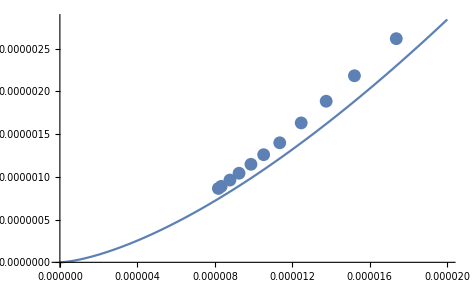

```mathematica
Show[Plot[√(1010 t^3),{t,0,0.00002}],ListPlot[data]]
```